# Modèle 3.5 : Parasitoïde de Nymphes αl = 0

## Présentation du modèle

```mathematica
ModeleComplet= {
U'[t] == q A[t] - δu U[t]- q A[t-τu] Exp[-δu τu],
L'[t] == q A[t-τu] Exp[-δu τu] -δl L[t] - q A[t-τu-τl]Exp[-δu τu]Exp[-δl τl],
M'[t] == q A[t-τu-τl]Exp[-δu τu] Exp[-δl τl] -a M[t]P[t]- δm M[t] - q A[t-τu-τl-τm]Exp[-δu τu] Exp[-δl τl]Hp[t],
A'[t] == q A[t-τu-τl-τm]Exp[-δu τu] Exp[-δl τl]Hp[t] -δa A[t],
J'[t] ==a M[t]P[t]-δj J[t]-a M[t-τj]P[t-τj] Exp[-δj τj],
P'[t] ==a M[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
Hp'[t] ==-a Hp[t](P[t]-P[t-τm])
}
ModelReduit = {
M'[t] == q A[t-τu-τl]Exp[-δu τu] Exp[-δl τl] -a M[t]P[t]- δm M[t] - q A[t-τu-τl-τm]Exp[-δu τu] Exp[-δl τl]Hp[t],
A'[t] == q A[t-τu-τl-τm]Exp[-δu τu] Exp[-δl τl]Hp[t] -δa A[t],
P'[t] ==a M[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
Hp'[t] ==-a Hp[t](P[t]-P[t-τm])
}
```

{U'[t]==q A[t]-ⅇ^(-δu τu) q A[t-τu]-δu U[t],L'[t]==ⅇ^(-δu τu) q A[t-τu]-ⅇ^(-δl τl-δu τu) q A[t-τl-τu]-δl L[t],M'[t]==ⅇ^(-δl τl-δu τu) q A[t-τl-τu]-ⅇ^(-δl τl-δu τu) q A[t-τl-τm-τu] Hp[t]-δm M[t]-a M[t] P[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δu τu) q A[t-τl-τm-τu] Hp[t],J'[t]==-δj J[t]+a M[t] P[t]-a ⅇ^(-δj τj) M[t-τj] P[t-τj],P'[t]==-δp P[t]+a ⅇ^(-δj τj) M[t-τj] P[t-τj],Hp'[t]==-a Hp[t] (P[t]-P[t-τm])}

{M'[t]==ⅇ^(-δl τl-δu τu) q A[t-τl-τu]-ⅇ^(-δl τl-δu τu) q A[t-τl-τm-τu] Hp[t]-δm M[t]-a M[t] P[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δu τu) q A[t-τl-τm-τu] Hp[t],P'[t]==-δp P[t]+a ⅇ^(-δj τj) M[t-τj] P[t-τj],Hp'[t]==-a Hp[t] (P[t]-P[t-τm])}

## Étude analytique

## Points fixes

### Valeur à l’équilibre des taux de mortalité non fixe

```mathematica
HpEqNnTri = Exp[-τm(δm+a Peq)];
```

```mathematica
HpIni= HpEqNnTri/.{Peq->1}
```

ⅇ^(-((a+δm) τm))

### Modèle à l’équilibre

```mathematica
ModelReduitEq = {
0 == q Aeq Exp[-δu τu] Exp[-δl τl] -a Meq Peq- δm Meq - q Aeq Exp[-δu τu] Exp[-δl τl]Hpeq,
0 == q Aeq Exp[-δu τu] Exp[-δl τl]Hpeq -δa Aeq,
0 ==a Meq Peq Exp[-δj τj]-δp Peq
}
```

{0==-a Meq Peq+Aeq ⅇ^(-δl τl-δu τu) q-Aeq ⅇ^(-δl τl-δu τu) Hpeq q-Meq δm,0==Aeq ⅇ^(-δl τl-δu τu) Hpeq q-Aeq δa,0==a ⅇ^(-δj τj) Meq Peq-Peq δp}

```mathematica
ModeleEq = {
0 == q Aeq - δu Ueq- q Aeq Exp[-δu τu],
0 == q Aeq Exp[-δu τu] -δl Leq - q Aeq Exp[-δu τu]Exp[-δl τl],
0 == q Aeq Exp[-δu τu] Exp[-δl τl] -a Meq Peq- δm Meq - q Aeq Exp[-δu τu] Exp[-δl τl]Hpeq,
0 == q Aeq Exp[-δu τu] Exp[-δl τl]Hpeq -δa Aeq,
0 ==a Meq Peq-δj Jeq-a Meq Peq Exp[-δj τj],
0 ==a Meq Peq Exp[-δj τj]-δp Peq
};
MatrixForm[ModeleEq /.{Hpeq->HpEqNnTri}]
```

(0==Aeq q-Aeq ⅇ^(-δu τu) q-Ueq δu
0==Aeq ⅇ^(-δu τu) q-Aeq ⅇ^(-δl τl-δu τu) q-Leq δl
0==-a Meq Peq+Aeq ⅇ^(-δl τl-δu τu) q-Aeq ⅇ^(-δl τl-(a Peq+δm) τm-δu τu) q-Meq δm
0==Aeq ⅇ^(-δl τl-(a Peq+δm) τm-δu τu) q-Aeq δa
0==a Meq Peq-a ⅇ^(-δj τj) Meq Peq-Jeq δj
0==a ⅇ^(-δj τj) Meq Peq-Peq δp)

### Résolution globale

```mathematica
Solve[ModeleEq /.{Hpeq->HpEqNnTri},{Ueq, Leq, Meq,Aeq,Jeq,Peq}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{}

### Résolution par parties

#### Recherche de Meq

```mathematica
MeqNnTri = Meq/.Solve[0==a ⅇ^(-δj τj) Meq Peq-Peq δp,Meq][[1]]
```

(ⅇ^(δj τj) δp)/a

#### Recherche de Peq

```mathematica
PeqNnTri = Peq/.Solve[0==Aeq ⅇ^(-δl τl-(a Peq+δm) τm-δu τu) q-Aeq δa,Peq][[1]]
PeqNnTri = (-δl τl-δm τm-δu τu+Log[q/δa])/(a τm)
```

ConditionalExpression[(-δl τl-δm τm-δu τu+2 ⅈ π C[1]+Log[q/δa])/(a τm), C[1]∈ℤ]

(-δl τl-δm τm-δu τu+Log[q/δa])/(a τm)

#### Recherche de Jeq

```mathematica
JeqNnTriBrut = Jeq/.Solve[0==a Meq Peq-a ⅇ^(-δj τj) Meq Peq-Jeq δj,Jeq][[1]]
JeqNnTri = JeqNnTriBrut/.{Meq->MeqNnTri,Peq->PeqNnTri}
```

(a ⅇ^(-δj τj) (-1+ⅇ^(δj τj)) Meq Peq)/δj

((-1+ⅇ^(δj τj)) δp (-δl τl-δm τm-δu τu+Log[q/δa]))/(a δj τm)

#### Recherche de Aeq

```mathematica
AeqNnTriBrut = Aeq/.Solve[0==-a Meq Peq+Aeq ⅇ^(-δl τl-δu τu) q-Aeq ⅇ^(-δl τl-(a Peq+δm) τm-δu τu) q-Meq δm,Aeq][[1]]
AeqNnTri=AeqNnTriBrut/.{Meq->MeqNnTri,Peq->PeqNnTri}
```

(ⅇ^(δl τl+(a Peq+δm) τm+δu τu) Meq (a Peq+δm))/((-1+ⅇ^((a Peq+δm) τm)) q)

(ⅇ^(δj τj+δl τl+δu τu+τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm)) δp (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))/(a (-1+ⅇ^(τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))) q)

#### Recherche de Leq

```mathematica
LeqNnTriBrut = Leq/.Solve[0==Aeq ⅇ^(-δu τu) q-Aeq ⅇ^(-δl τl-δu τu) q-Leq δl,Leq][[1]]
LeqNnTri = LeqNnTriBrut/.{Aeq->AeqNnTri}
```

(Aeq ⅇ^(-δl τl-δu τu) (-1+ⅇ^(δl τl)) q)/δl

(ⅇ^(δj τj+τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm)) (-1+ⅇ^(δl τl)) δp (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))/(a (-1+ⅇ^(τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))) δl)

#### Recherche de Ueq

```mathematica
UeqNnTriBrut = Ueq/.Solve[0==Aeq q-Aeq ⅇ^(-δu τu) q-Ueq δu,Ueq][[1]]
UeqNnTri = UeqNnTriBrut/.{Aeq->AeqNnTri}
```

(Aeq ⅇ^(-δu τu) (-1+ⅇ^(δu τu)) q)/δu

(ⅇ^(δj τj+δl τl+τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm)) (-1+ⅇ^(δu τu)) δp (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))/(a (-1+ⅇ^(τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))) δu)

#### Recherche de Heq

```mathematica
HpeqNnTriFinal = HpEqNnTri/.{Peq->PeqNnTri}
```

ⅇ^(-τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))

#### Récap des valeur à l’eq

```mathematica
UeqNnTriBrut
LeqNnTriBrut
MeqNnTri
AeqNnTriBrut
JeqNnTriBrut
PeqNnTri
HpeqNnTriFinal
```

(Aeq ⅇ^(-δu τu) (-1+ⅇ^(δu τu)) q)/δu

(Aeq ⅇ^(-δl τl-δu τu) (-1+ⅇ^(δl τl)) q)/δl

(ⅇ^(δj τj) δp)/a

(ⅇ^(δl τl+(a Peq+δm) τm+δu τu) Meq (a Peq+δm))/((-1+ⅇ^((a Peq+δm) τm)) q)

(a ⅇ^(-δj τj) (-1+ⅇ^(δj τj)) Meq Peq)/δj

(-δl τl-δm τm-δu τu+Log[q/δa])/(a τm)

ⅇ^(-τm (δm+(-δl τl-δm τm-δu τu+Log[q/δa])/τm))

### Vérification

```mathematica
ModeleEq/.{Hpeq->HpeqNnTriFinal,Ueq->UeqNnTri,Leq->LeqNnTri,Meq->MeqNnTri,Aeq->AeqNnTri,Jeq->JeqNnTri,Peq->PeqNnTri}//FullSimplify
```

{True,True,True,True,True,True}

Après miiiiiiiiiille ans : On est bon !!!!

### Condition d’existence des points fixes

```mathematica
Solve[0==PeqNnTri,q]
Solve[0==PeqNnTri,δu]/.{δl->0,δa->0.1,δm->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δl]/.{δu->0,δa->0.1,δm->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δm]/.{δl->0,δa->0.1,δu->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δa]/.{δl->0,δu->0,δm->0,τu->4,τl->16,τm->8}
```

{{q→ConditionalExpression[ⅇ^(δl τl+δm τm+δu τu) δa, -π<Im[δl τl+δm τm+δu τu]≤π]}}

{{δu→1/4 Log[10. q]}}

{{δl→1/16 Log[10. q]}}

{{δm→1/8 Log[10. q]}}

{{δa→q}}

### Conclusion Point Fixe

Possibilité de trouver les points fixes et leur condition d’existance

## Diagramme de Bifurcation Analytique

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;δjN=δmN; τjN=τmN;δpN=8;aN=1;qN=106.4/12.2;δaN=1/12.2;αlN=0.001;
```

### Initialisation

```mathematica
UeqNnTriV = UeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δm,τj->τjN,δp->δpN,a->aN}
LeqNnTriV = LeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δm,τj->τjN,δp->δpN,a->aN}
MeqNnTriV = MeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δm,τj->τjN,δp->δpN,a->aN}
AeqNnTriV = AeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δm,τj->τjN,δp->δpN,a->aN}
JeqNnTriV = JeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δm,τj->τjN,δp->δpN,a->aN}
PeqNnTriV = PeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δm,τj->τjN,δp->δpN,a->aN}
```

(41.8853 ⅇ^(0.0768+8.92 δm+8.92 (0.112108 (4.3865-8.92 δm)+δm)) (0.112108 (4.3865-8.92 δm)+δm))/(-1+ⅇ^(8.92 (0.112108 (4.3865-8.92 δm)+δm)))

(133.043 ⅇ^(8.92 δm+8.92 (0.112108 (4.3865-8.92 δm)+δm)) (0.112108 (4.3865-8.92 δm)+δm))/(-1+ⅇ^(8.92 (0.112108 (4.3865-8.92 δm)+δm)))

8 ⅇ^(8.92 δm)

(0.917293 ⅇ^(0.280704+8.92 δm+8.92 (0.112108 (4.3865-8.92 δm)+δm)) (0.112108 (4.3865-8.92 δm)+δm))/(-1+ⅇ^(8.92 (0.112108 (4.3865-8.92 δm)+δm)))

(0.896861 (-1+ⅇ^(8.92 δm)) (4.3865-8.92 δm))/δm

0.112108 (4.3865-8.92 δm)

```mathematica
bifurcationU=Table[
{δm, UeqNnTriV},
{δm,0.0001,1,0.0001}
];
bifurcationL=Table[
{δm, LeqNnTriV},
{δm,0.0001,1,0.0001}
];
bifurcationM=Table[
{δm, MeqNnTriV},
{δm,0.0001,1,0.0001}
];
bifurcationA=Table[
{δm, AeqNnTriV},
{δm,0.0001,1,0.0001}
];
bifurcationJ=Table[
{δm, JeqNnTriV},
{δm,0.0001,1,0.0001}
];
bifurcationP=Table[
{δm, PeqNnTriV},
{δm,0.0001,1,0.0001}
];
```

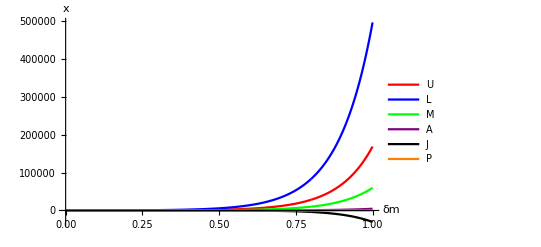

```mathematica
ListLinePlot[
{bifurcationU,bifurcationL,bifurcationM,bifurcationA,bifurcationJ,bifurcationP},
PlotStyle->{Red,Blue,Green,Purple,Black,Orange},
PlotLegends->{"U","L","M","A","J","P"},
AxesLabel->{"δm","x"},PlotRange->All]
```

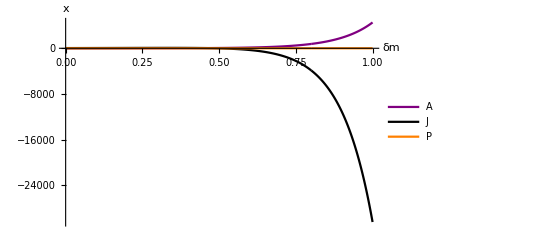

```mathematica
ListLinePlot[
{bifurcationA,bifurcationJ,bifurcationP},
PlotStyle->{Purple,Black,Orange},
PlotLegends->{"A","J","P"},
AxesLabel->{"δm","x"},PlotRange->All]
```

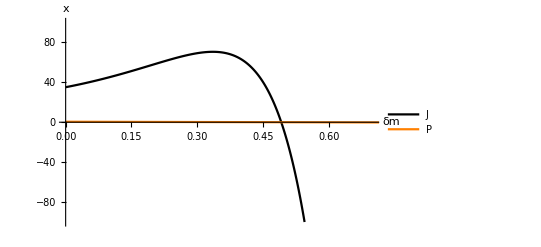

```mathematica
ListLinePlot[
{bifurcationJ,bifurcationP},
PlotStyle->{Black,Orange},
PlotLegends->{"J","P"},
AxesLabel->{"δm","x"},PlotRange->{{0,0.7},{-100,100}}]
```

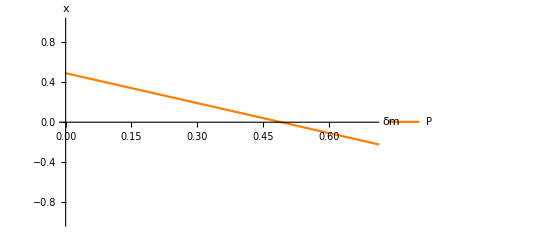

```mathematica
ListLinePlot[
{bifurcationP},
PlotStyle->{Orange},
PlotLegends->{"P"},
AxesLabel->{"δm","x"},PlotRange->{{0,0.7},{-1,1}}]
```

### Conclusion

## Linéarisation

```mathematica
ModeleLineaire = {
nM'[t] == q nA[t-τu-τl]Exp[-δu τu] Exp[-δl τl] -a nM[t]Peq-a Meq nP[t]- δm nM[t] - q nA[t-τu-τl-τm]Exp[-δu τu] Exp[-δl τl]Hpeq- q Aeq Exp[-δu τu] Exp[-δl τl]nHp[t],
nA'[t] == q nA[t-τu-τl-τm]Exp[-δu τu] Exp[-δl τl]Hpeq+q Aeq Exp[-δu τu] Exp[-δl τl]nHp[t] -δa nA[t],
nP'[t] ==a nM[t-τj]Peq Exp[-δj τj]+a Meq nP[t-τj] Exp[-δj τj]-δp nP[t],
nHp'[t] ==-a Hpeq(nP[t]-nP[t-τm])
}
```

{nM'[t]==ⅇ^(-δl τl-δu τu) q nA[t-τl-τu]-ⅇ^(-δl τl-δu τu) Hpeq q nA[t-τl-τm-τu]-Aeq ⅇ^(-δl τl-δu τu) q nHp[t]-a Peq nM[t]-δm nM[t]-a Meq nP[t],nA'[t]==-δa nA[t]+ⅇ^(-δl τl-δu τu) Hpeq q nA[t-τl-τm-τu]+Aeq ⅇ^(-δl τl-δu τu) q nHp[t],nP'[t]==a ⅇ^(-δj τj) Peq nM[t-τj]-δp nP[t]+a ⅇ^(-δj τj) Meq nP[t-τj],nHp'[t]==-a Hpeq (nP[t]-nP[t-τm])}

## Transformation de Laplace

```mathematica
ModeleLaplace = {
-s M[s] + q A[s]Exp[-s τu-s τl]Exp[-δu τu] Exp[-δl τl] -a M[s]Peq-a Meq P[s]- δm M[s] - q A[s]Exp[-s τu-s τl-s τm]Exp[-δu τu] Exp[-δl τl]Hpeq- q Aeq Exp[-δu τu] Exp[-δl τl]Hp[s],
-s A[s] + q A[s]Exp[-s τu-s τl-s τm]Exp[-δu τu] Exp[-δl τl]Hpeq+q Aeq Exp[-δu τu] Exp[-δl τl]Hp[s] -δa A[s],
-s P[s] +a M[s] Exp[-s τj]Peq Exp[-δj τj]+a Meq P[s] Exp[-s τj] Exp[-δj τj]-δp P[s],
-s Hp[s]-a Hpeq(P[s]-P[s]Exp[-s τm])
}
```

{ⅇ^(-s τl-δl τl-s τu-δu τu) q A[s]-ⅇ^(-s τl-δl τl-s τm-s τu-δu τu) Hpeq q A[s]-Aeq ⅇ^(-δl τl-δu τu) q Hp[s]-a Peq M[s]-s M[s]-δm M[s]-a Meq P[s],ⅇ^(-s τl-δl τl-s τm-s τu-δu τu) Hpeq q A[s]-s A[s]-δa A[s]+Aeq ⅇ^(-δl τl-δu τu) q Hp[s],a ⅇ^(-s τj-δj τj) Peq M[s]+a ⅇ^(-s τj-δj τj) Meq P[s]-s P[s]-δp P[s],-s Hp[s]-a Hpeq (P[s]-ⅇ^(-s τm) P[s])}

## Jacobienne

```mathematica
JacobienneGeneral =  D[ModeleLaplace,{{M[s],A[s],P[s], Hp[s]}}];
MatrixForm[JacobienneGeneral]
```

(-a Peq-s-δm | ⅇ^(-s τl-δl τl-s τu-δu τu) q-ⅇ^(-s τl-δl τl-s τm-s τu-δu τu) Hpeq q | -a Meq | -Aeq ⅇ^(-δl τl-δu τu) q
0 | ⅇ^(-s τl-δl τl-s τm-s τu-δu τu) Hpeq q-s-δa | 0 | Aeq ⅇ^(-δl τl-δu τu) q
a ⅇ^(-s τj-δj τj) Peq | 0 | a ⅇ^(-s τj-δj τj) Meq-s-δp | 0
0 | 0 | -a (1-ⅇ^(-s τm)) Hpeq | -s)

```mathematica
JacobienneEqNnTri = FullSimplify[JacobienneGeneral/.{Aeq->AeqNnTri,Meq->MeqNnTri,Peq->PeqNnTri, Hpeq->(HpEqNnTri/.Peq ->PeqNnTri)}]
```

{{(δl τl-s τm+δu τu-Log[q/δa])/τm,ⅇ^(-s (τl+τm+τu)) (ⅇ^(-δl τl+s τm-δu τu) q-δa),-ⅇ^(δj τj) δp,(ⅇ^(δj τj) q δp (δl τl+δu τu-Log[q/δa]))/(a (q-ⅇ^(δl τl+δu τu) δa) τm)},{0,-s+(-1+ⅇ^(-s (τl+τm+τu))) δa,0,(ⅇ^(δj τj) q δp (δl τl+δu τu-Log[q/δa]))/(a (-q+ⅇ^(δl τl+δu τu) δa) τm)},{-(ⅇ^(-((s+δj) τj)) (δl τl+δm τm+δu τu-Log[q/δa]))/τm,0,-s+(-1+ⅇ^(-s τj)) δp,0},{0,0,-(a ⅇ^(δl τl-s τm+δu τu) (-1+ⅇ^(s τm)) δa)/q,-s}}

## *Stabilité*

### Point Fixe trivial

### Point Fixe non trivial

## Équation caractéristique et sa transformation

```mathematica
EquationCaracteristique = Det[JacobienneEqNnTri]
```

-s (-s+(-1+ⅇ^(-s (τl+τm+τu))) δa) (((-s+(-1+ⅇ^(-s τj)) δp) (δl τl-s τm+δu τu-Log[q/δa]))/τm-(ⅇ^(δj τj-(s+δj) τj) δp (δl τl+δm τm+δu τu-Log[q/δa]))/τm)-(a ⅇ^(-((s+δj) τj)+δl τl-s τm+δu τu) (-1+ⅇ^(s τm)) δa ((ⅇ^(δj τj-s (τl+τm+τu)) q (ⅇ^(-δl τl+s τm-δu τu) q-δa) δp (δl τl+δu τu-Log[q/δa]))/(a (-q+ⅇ^(δl τl+δu τu) δa) τm)-(ⅇ^(δj τj) q (-s+(-1+ⅇ^(-s (τl+τm+τu))) δa) δp (δl τl+δu τu-Log[q/δa]))/(a (q-ⅇ^(δl τl+δu τu) δa) τm)) (δl τl+δm τm+δu τu-Log[q/δa]))/(q τm)

### Focus sur les solution avec Réel Nul

```mathematica
EquationCaracteristiqueI =EquationCaracteristique /.{s->I x}
```

-ⅈ x (-ⅈ x+(-1+ⅇ^(-ⅈ x (τl+τm+τu))) δa) (((-ⅈ x+(-1+ⅇ^(-ⅈ x τj)) δp) (δl τl-ⅈ x τm+δu τu-Log[q/δa]))/τm-(ⅇ^(δj τj-(ⅈ x+δj) τj) δp (δl τl+δm τm+δu τu-Log[q/δa]))/τm)-(a ⅇ^(-((ⅈ x+δj) τj)+δl τl-ⅈ x τm+δu τu) (-1+ⅇ^(ⅈ x τm)) δa ((ⅇ^(δj τj-ⅈ x (τl+τm+τu)) q (ⅇ^(-δl τl+ⅈ x τm-δu τu) q-δa) δp (δl τl+δu τu-Log[q/δa]))/(a (-q+ⅇ^(δl τl+δu τu) δa) τm)-(ⅇ^(δj τj) q (-ⅈ x+(-1+ⅇ^(-ⅈ x (τl+τm+τu))) δa) δp (δl τl+δu τu-Log[q/δa]))/(a (q-ⅇ^(δl τl+δu τu) δa) τm)) (δl τl+δm τm+δu τu-Log[q/δa]))/(q τm)

```mathematica
eqCaraRe = ComplexExpand[Re[EquationCaracteristiqueI]];
eqCaraIm = ComplexExpand[Im[EquationCaracteristiqueI]];
```

## Étude numérique

## Import et paramètres

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;δuN=0.0432;δlN=0.0048;δmN=0.0150;δpN=8;δjN=δlN;τjN=τlN;aN=1;
```

### Gamme de δa et q

```mathematica
δaMin =0.001; δaMax = 1; δaPas = 0.001;
qMin =0; qMax = 10; qPas = 0.01;

δaRangeInv=Range[δaMax,δaMin,-δaPas];
δaRange=Range[δaMin,δaMax,δaPas];
qRange=Range[qMin,qMax,qPas];
```

### Fixation des paramètres

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraReδm= eqCaraRe/.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δa->δaN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImδm = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δa->δaN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraReδu= eqCaraRe/.{τu ->τuN,τl ->τlN,τm ->τmN,δm ->δmN,δl->δlN,δa->δaN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImδu= eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δm ->δmN,δl->δlN,δa->δaN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraReδl= eqCaraRe/.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δm->δmN,δa->δaN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImδl= eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δm->δmN,δa->δaN,δp->δpN,δj->δjN,τj->τjN,a->aN};
```

## Limite de stabilité en fonction de δa et q

#### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δa->1},eqCaraImEq/.{δa->1}},{x,0.4},{q,1}]
FindRoot[{eqCaraReEq/.{δa->0.001},eqCaraImEq/.{δa->0.001}},{x,0.4},{q,100}]
```

{x→0.389967,q→1.4696}

{x→0.389519,q→0.00150269}

#### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;    CourbeLimiteCompJulia3 = {}  ;  
ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =0.3899666530004783;
xtempo =1.4695990450844276;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δa}];
,{δa,δaMax,δaMin,-0.0001}] 

ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =0.0015026859949333962;
xtempo =0.389519110906773 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δa}];
,{δa,δaMin,δaMax,δaPas}] 

ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =30;
xtempo =1 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia3,{qtempo,δa}];
,{δa,δaMin,δaMax,δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

### Tracé de la limite de stabilité en fonction de δa et q

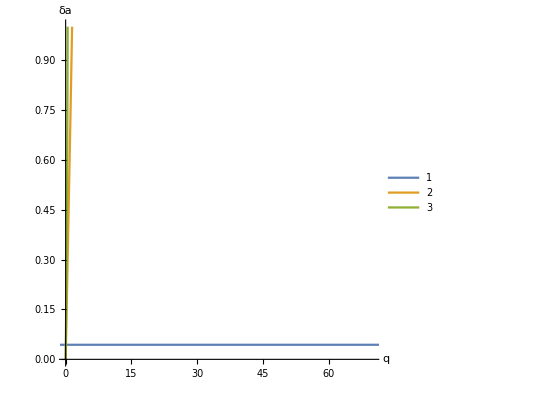

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2,CourbeLimiteCompJulia3},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}}
]
```

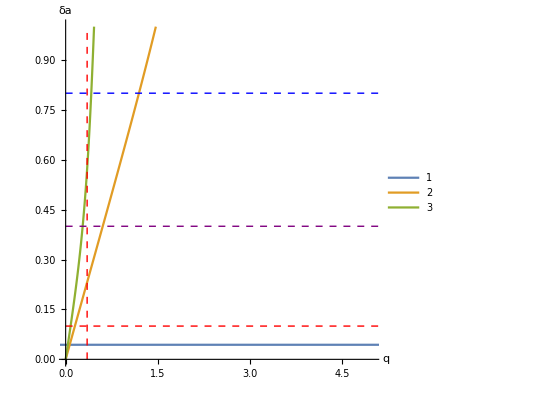

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2,CourbeLimiteCompJulia3},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,5},{0,1}},
Epilog->{{Red,Dashed,Line[{{0.35,0},{0.35,1}}]},
{Red,Dashed,Line[{{0,0.1},{100,0.1}}]},
{Purple,Dashed,Line[{{0,0.4},{100,0.4}}]},
{Blue,Dashed,Line[{{0,0.8},{100,0.8}}]}
}
]
```

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaA1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaA2.csv",CourbeLimiteCompJulia2,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaA3.csv",CourbeLimiteCompJulia3,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaA1.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaA2.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaA3.csv

#### Comparaison aux dynamiques

```mathematica
tmax = 1000;
```

#### Red line

NDSolve::ndstf: At t == 1840.56, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

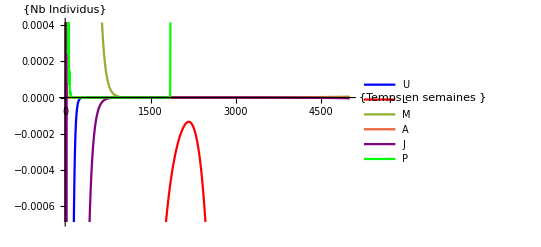

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.35,δa->1,αl->αlN,δj->δmN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==0.1,Hp[t/;t<=0]==HpIni/.{δm ->δmN,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

#### Purple line

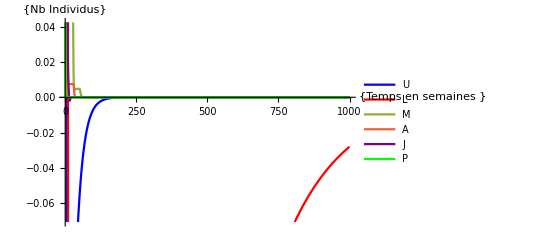

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> 0.4,τu -> τuN, τl -> τlN, τm-> τmN,q->0.35,δa->1,αl->αlN,δj->0.4,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->0.4,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

#### Blue line

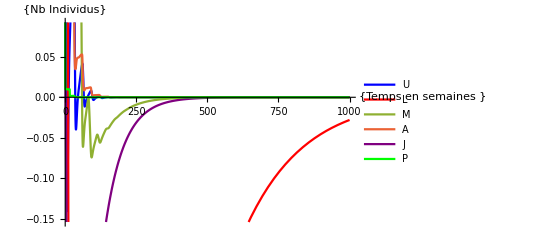

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm ->δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.35,δa->1,αl->αlN,δj->δmN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==0.1,P[t/;t<=0]==0.1,Hp[t/;t<=0]==HpIni/.{δm ->δmN,τm -> τmN,a->aN*0.1}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

#### p =0.2

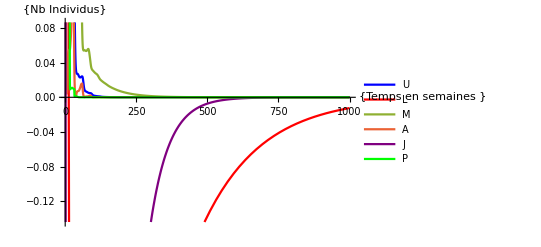

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.2,δa->1,αl->αlN,δj->δmN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->δmN,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

#### p =1

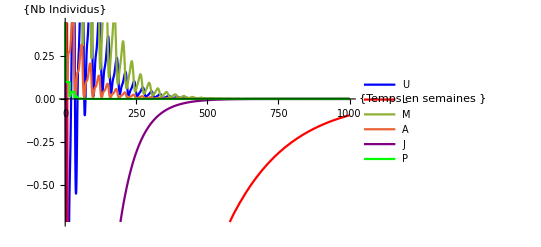

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->1,δa->1,αl->αlN,δj->δmN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->δmN,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

#### p =2

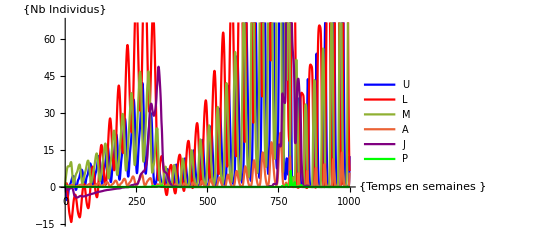

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->2,δa->1,αl->αlN,δj->δmN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->δmN,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

Pour δa = 1, le PF est instable pour q=0.1 et 1, cela laisserai entendre que la jolie limite de stab verte serrai fausse et pas de preuve pour la bleu

## Limite de stabilité en fonction de δm et q

#### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReδm/.{δm->0.01},eqCaraImδm/.{δm->0.01}},{x,3},{q,1}]
FindRoot[{eqCaraReδm/.{δm->1},eqCaraImδm/.{δm->1}},{x,3},{q,1}]
```

{x→3.10593,q→0.000187438}

{x→3.09933,q→0.0826409}

#### Calcule des points

```mathematica
CourbeLimiteCompJuliaδm1 = {}  ;  CourbeLimiteCompJuliaδm2 = {}  ; 
ClearAll[qtempo, xtempo,δm,q,root,  x]
qtempo =3;
xtempo =1;
Do [
root = FindRoot[{eqCaraReδm,eqCaraImδm},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJuliaδm1,{qtempo,δm}];
,{δm,0.01,1,0.01}] 

ClearAll[qtempo, xtempo,δm,q,root,  x]
qtempo =1;
xtempo =3;
Do [
root = FindRoot[{eqCaraReδm,eqCaraImδm},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJuliaδm2,{qtempo,δm}];
,{δm,1,0.01,-0.01}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

## Affichage des résultats

### Tracé de la limite de stabilité en fonction de δm et q

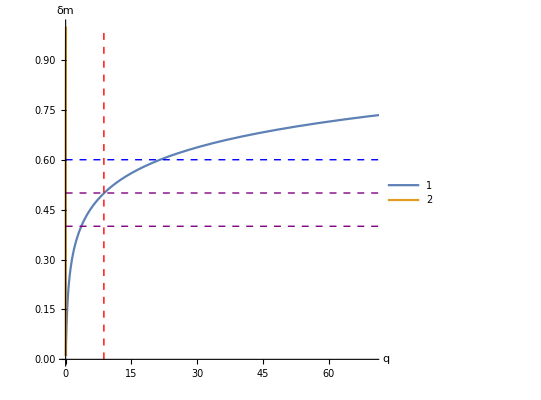

```mathematica
ListLinePlot[{CourbeLimiteCompJuliaδm1,CourbeLimiteCompJuliaδm2},
Axes->True,
AxesLabel -> {"q","δm"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Epilog->{{Red,Dashed,Line[{{qN,0},{qN,1}}]},
{Purple,Dashed,Line[{{0,0.4},{100,0.4}}]},
{Purple,Dashed,Line[{{0,0.5},{100,0.5}}]},
{Blue,Dashed,Line[{{0,0.6},{100,0.6}}]},
}
]
```

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaM1.csv",CourbeLimiteCompJuliaδm1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaM2.csv",CourbeLimiteCompJuliaδm2,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaM1.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaM2.csv

```mathematica
tmax =1000;
```

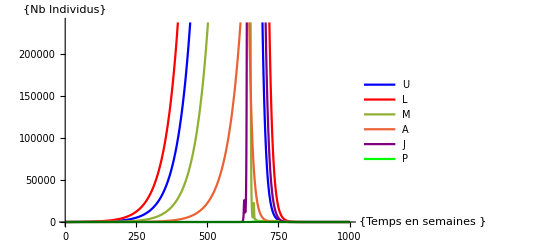

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> 0.4,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->0.4,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->0.4,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

$Aborted

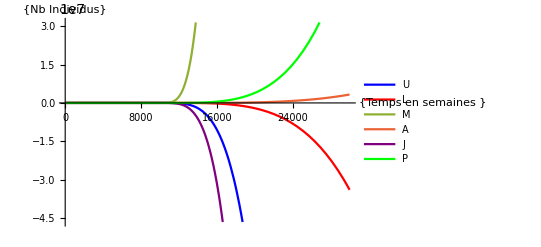

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> 0.49,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->0.49,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->0.49,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

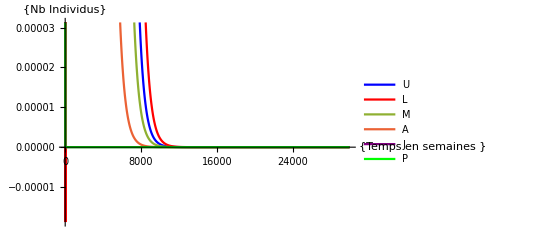

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> 0.5,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->0.5,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->0.5,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

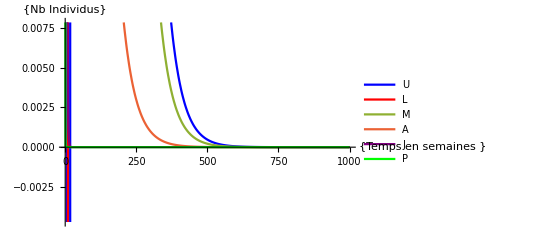

```mathematica
solN=NDSolve[{ModeleComplet/.{δu ->δuN,δl -> δlN, δm -> 0.6,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->0.6,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,M[t/;t<=0]==1,A[t/;t<=0]==1,J[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==HpIni/.{δm ->0.6,τm -> τmN,a->aN}},{U,L, M,A,J,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],M[t],A[t],J[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","M","A","J","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}},PlotStyle->{Blue,(*Couleur de U[t]*)Red,(*Couleur de L[t]*),Orange(*Couleur de M[t]*)Black,(*Couleur de A[t]*)Purple,(*Couleur de J[t]*) Green    (*Couleur de P[t]*)}]
```

## Limite de stabilité en fonction de δu et q

#### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReδu/.{δu->1},eqCaraImδu/.{δu->1}},{x,7},{q,30}]
FindRoot[{eqCaraReδu/.{δu->0.001},eqCaraImδu/.{δu->0.001}},{x,0.4},{q,3}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→7.0222,q→3.97631}

{x→0.389553,q→0.101157}

#### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;    CourbeLimiteCompJulia3 = {}  ;  
ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =11.293207707639146;
xtempo =0.38955348462181405;
Do [
root = FindRoot[{eqCaraReδu,eqCaraImδu},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δu}];
,{δu,δaMax,δaMin,-0.0001}] 

ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =0.10115730051600527;
xtempo =0.3895534846218129 ;
Do [
root = FindRoot[{eqCaraReδu,eqCaraImδu},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δu}];
,{δu,δaMin,δaMax,δaPas}] 

ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =30;
xtempo =1 ;
Do [
root = FindRoot[{eqCaraReδu,eqCaraImδu},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia3,{qtempo,δu}];
,{δu,δaMin,δaMax,δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

### Tracé de la limite de stabilité en fonction de δu et q

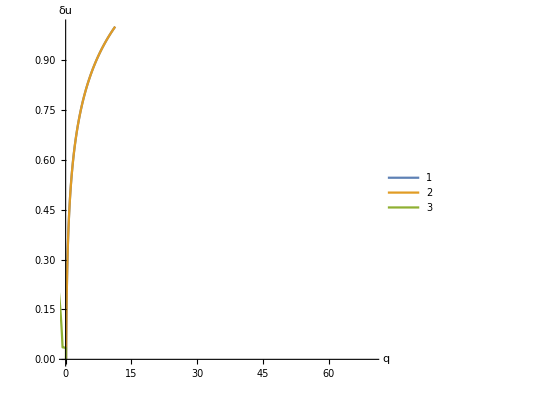

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2,CourbeLimiteCompJulia3},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}}
]
```

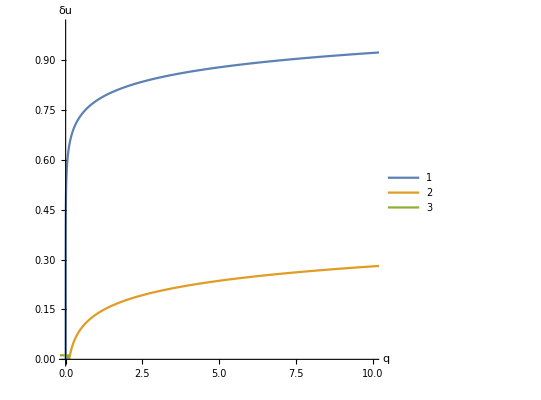

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2,CourbeLimiteCompJulia3},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,10},{0,1}}
]
```

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaU1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaU2.csv",CourbeLimiteCompJulia2,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaU3.csv",CourbeLimiteCompJulia3,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaU1.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaU2.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaU3.csv

## Limite de stabilité en fonction de δl et q

#### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReδl/.{δl->1},eqCaraImδl/.{δl->1}},{x,0.8},{q,1}]
FindRoot[{eqCaraReδl/.{δl->0.001},eqCaraImδl/.{δl->0.001}},{x,0.4},{q,4}]
```

{x→0.768056,q→35.3567}

{x→0.389553,q→0.116171}

#### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;    CourbeLimiteCompJulia3 = {}  ;  
ClearAll[qtempo, xtempo,δl,q,root,  x]
qtempo =35.35672221812496;
xtempo =0.7680564656563587;
Do [
root = FindRoot[{eqCaraReδl,eqCaraImδl},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δl}];
,{δl,δaMax,δaMin,-0.0001}] 

ClearAll[qtempo, xtempo,δl,q,root,  x]
qtempo =0.11617070871231894;
xtempo =0.38955348462181294 ;
Do [
root = FindRoot[{eqCaraReδl,eqCaraImδl},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δl}];
,{δl,δaMin,δaMax,δaPas}] 

ClearAll[qtempo, xtempo,δl,q,root,  x]
qtempo =30;
xtempo =1 ;
Do [
root = FindRoot[{eqCaraReδl,eqCaraImδl},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia3,{qtempo,δl}];
,{δl,δaMin,δaMax,δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

### Tracé de la limite de stabilité en fonction de δl et q

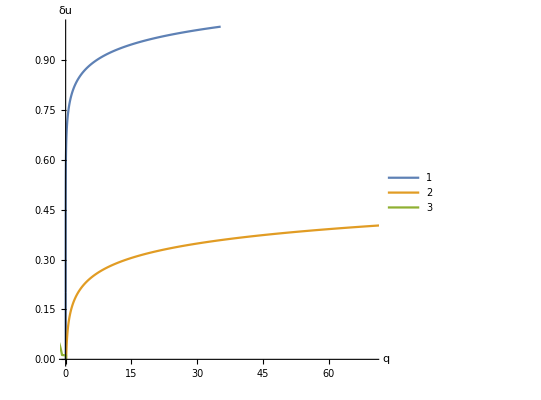

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2,CourbeLimiteCompJulia3},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,Ò
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}}
]
```

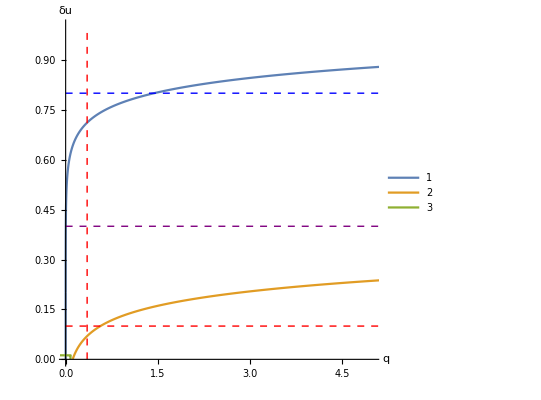

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2,CourbeLimiteCompJulia3},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,5},{0,1}},
Epilog->{{Red,Dashed,Line[{{0.35,0},{0.35,1}}]},
{Red,Dashed,Line[{{0,0.1},{100,0.1}}]},
{Purple,Dashed,Line[{{0,0.4},{100,0.4}}]},
{Blue,Dashed,Line[{{0,0.8},{100,0.8}}]}
}
]
```

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaL1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaL2.csv",CourbeLimiteCompJulia2,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaL3.csv",CourbeLimiteCompJulia3,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaL1.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaL2.csv

/Users/Quentin/Desktop/Article1/tables/ParaNymphe/LimiteStabDeltaL3.csv

## Comparaison de dynamique avec Julia

### Paramétrisation

### Recherche de valeur d’initialisation du FindRoot

### Création des Courbes

### Affichage des résultats

## Dynamiques

## Comparaison de dynamique avec Julia

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1, Hc[t/;t<=0]==1,Hp[t/;t<=0]==1},{U,L,A,P,Hc,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],A[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","A","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

NDSolve::ndstf: At t == 6.16698, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

$Aborted

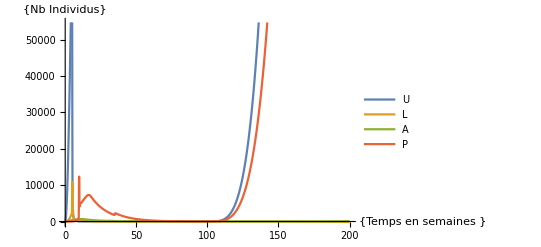

```mathematica
solN=NDSolve[{ModeleQuentin/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1, Hc[t/;t<=0]==0,Hp[t/;t<=0]==0},{U,L,A,P,Hc,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],A[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","A","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```